```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{118,267}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20,4/21/20,4/22/20,4/23/20,4/24/20,4/25/20,4/26/20,4/27/20,4/28/20,4/29/20,4/30/20,5/1/20,5/2/20,5/3/20,5/4/20,5/5/20,5/6/20,5/7/20,5/8/20,5/9/20,5/10/20,5/11/20,5/12/20,5/13/20,5/14/20,5/15/20}

115

{267}

```mathematica
TableForm[series];
```

```mathematica
TableForm[s];
```

```mathematica
CountryData["Japan","Population"]
```

126225259

```mathematica
{"Singapore",200,{2.835279843883035*^8,64.38918662693713,0.1259411788554341},21,7,10,0},
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0},
```

```mathematica
countryparameters=
(*name,truncdrop,jp0,lag,projtime,bootlag,plotdrop*)
{
{"Spain",300,{220179.72743729973,3738.260142762334,0.140854450046756},28,21,5,0},{"Canada",200,{81077.39354813701,1942.4785517808518,0.09614986026664779},21,21,10,0},{"Australia",100,{6739.694777539763,109.80989304529129,0.2176890747257849},28,21,3,0},{"New Zealand",5,{1474.4790552718507,17.837297202136803,0.22787919159710443},21,21,10,0},{"Croatia",10,{2136.3445533928943,31.72191300732455,0.14074152304198262},28,21,3,0},{"Czechia",10,{7901.635972368201,127.858460333728,0.13557437401035852},21,21,10,0},{"Sweden",200,{31272.793301689162,709.071763360148,0.08355406779130738},28,21,10,0},{"Greece",50,{2666.2946598125536,129.93576587902731,0.11994181591439824},28,21,10,0},{"Japan",950,{16302.099406766767,451.80679351636303,0.1327048660761382},28,21,8,0},{"Denmark",1100,{10976.989187588755,1103.472360444931,0.09290172311994832},28,21,10,0},{"Russia",300,{369442.4708046471,1404.1124969291448,0.114562446419243},21,21,10,0},{"United Kingdom",200,{242613.6018213363,2637.774825046479,0.10113748577252618},21,14,10,0},{"Hungary",50,{3497.602134723886,112.69091970270172,0.10969692792738958},28,21,10,0},{"France",300,{177843.2636752088,1554.9147679208638,0.1371138414227038},28,21,10,0},{"Singapore",900,{26421.784728354156,555.472525673107,0.1403556555382898},28,21,5,0},{"Serbia",50,{10410.396290570648,127.16306680915262,0.13621047340777273},21,21,10,0},{"Poland",50,{17709.029565845885,459.31825489863706,0.09649995071438171},21,21,5,0}
}
```

{{Spain,300,{220180.,3738.26,0.140854},28,21,5,0},{Canada,200,{81077.4,1942.48,0.0961499},21,21,10,0},{Australia,100,{6739.69,109.81,0.217689},28,21,3,0},{New Zealand,5,{1474.48,17.8373,0.227879},21,21,10,0},{Croatia,10,{2136.34,31.7219,0.140742},28,21,3,0},{Czechia,10,{7901.64,127.858,0.135574},21,21,10,0},{Sweden,200,{31272.8,709.072,0.0835541},28,21,10,0},{Greece,50,{2666.29,129.936,0.119942},28,21,10,0},{Japan,950,{16302.1,451.807,0.132705},28,21,8,0},{Denmark,1100,{10977.,1103.47,0.0929017},28,21,10,0},{Russia,300,{369442.,1404.11,0.114562},21,21,10,0},{United Kingdom,200,{242614.,2637.77,0.101137},21,14,10,0},{Hungary,50,{3497.6,112.691,0.109697},28,21,10,0},{France,300,{177843.,1554.91,0.137114},28,21,10,0},{Singapore,900,{26421.8,555.473,0.140356},28,21,5,0},{Serbia,50,{10410.4,127.163,0.13621},21,21,10,0},{Poland,50,{17709.,459.318,0.0965},21,21,5,0}}

```mathematica
Export["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml",countryparameters]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml

```mathematica
countryparameters=Import["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml"]
```

{{Spain,300,{220180.,3738.26,0.140854},28,21,10,0},{Canada,200,{81077.4,1942.48,0.0961499},21,21,10,0},{Australia,100,{6739.69,109.81,0.217689},28,21,5,0},{New Zealand,5,{1474.48,17.8373,0.227879},21,21,10,0},{Croatia,10,{2136.34,31.7219,0.140742},28,21,5,5},{Czechia,10,{7901.64,127.858,0.135574},21,21,10,5},{Sweden,200,{31272.8,709.072,0.0835541},28,21,10,0},{Greece,50,{2666.29,129.936,0.119942},28,21,10,0},{Japan,950,{16302.1,451.807,0.132705},28,21,8,0},{Denmark,1100,{10977.,1103.47,0.0929017},28,21,10,0},{Russia,300,{369442.,1404.11,0.114562},21,21,10,0},{United Kingdom,200,{242614.,2637.77,0.101137},21,14,10,0},{Hungary,50,{3497.6,112.691,0.109697},28,21,10,0},{France,300,{177843.,1554.91,0.137114},28,21,10,0},{Singapore,900,{26421.8,555.473,0.140356},28,21,5,0},{Serbia,50,{10410.4,127.163,0.13621},21,21,10,0},{Poland,50,{17709.,459.318,0.0965},21,21,5,0}}

```mathematica
"Spain",
```

```mathematica
wolfcountrynames={"Spain","Canada","Australia","New Zealand","Croatia","CzechRepublic","Sweden","Greece","Japan","Denmark","Russia","United Kingdom","Hungary","France","Singapore","Serbia","Poland"};
wpopulations=Map[CountryData[#,"Population"][[1]]&,wolfcountrynames]
lesscountrynames={};
morecountrynames={};
countrybootabcs={};
lesscountrybootabcs={};
morecountrybootabcs={};
```

{47290504,35309555,23502754,4554858,4369961,10611300,9595619,11470255,126225259,5628958,142400066,63556184,9918377,64101308,5336859,7164132,38344752}

```mathematica
lesscountrybootabcs={};
morecountrybootabcs={};
```

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump

country : Spain

data length : 71

start date : {2020,3,6}

jdp0 : {221392.,3873.82,0.139196}

jp20 : {264230.,115578.,0.0303779}

backward result : {149173.,836.891,0.222881}

forward result : {264230.,115578.,0.0303779}

last tab: {264230.,115578.,0.0303779}

backward result : {149173.,836.891,0.222881}

forward result : {264230.,115578.,0.0303779}

past errors : {{6097.59,6480.47,6956.07,7642.28,8142.38},7063.76}

boot tab : {{172500.,1258.76,0.197949},{176617.,1378.79,0.192869},{179254.,1485.19,0.188962},{183620.,1642.46,0.18352},{188727.,1847.32,0.177289},{192232.,2026.26,0.172606},{193558.,2141.66,0.17003},{193533.,2212.62,0.168765},{198037.,2547.58,0.162066},{207520.,3258.43,0.150253},{218019.,4238.36,0.138119},{219953.,4707.99,0.133981},{236503.,6667.92,0.118468},{240977.,7775.16,0.112536},{249201.,9634.66,0.104094},{256305.,11536.,0.0971699},{269689.,14429.6,0.0881561},{233787.,9590.26,0.107785},{230537.,9466.48,0.109144},{225944.,8895.11,0.112503},{222191.,8262.96,0.116059},{217969.,7175.07,0.121905},{220479.,8027.19,0.117632},{220472.,7833.18,0.118321},{221527.,7967.28,0.117325},{222057.,7714.,0.11787},{222296.,7325.42,0.119042},{222119.,6780.69,0.121079},{223159.,7084.36,0.119294},{223751.,6991.31,0.119169},{224643.,7271.66,0.117544},{226132.,8357.18,0.113128},{227228.,9415.97,0.109501},{228679.,11984.9,0.102875},{237152.,33270.6,0.0736954},{249636.,69988.1,0.0492689},{289698.,116876.,0.0254411},{1.27623×10^6,148544.,0.00749439},{1.90298×10^8,152053.,0.00604651}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71}

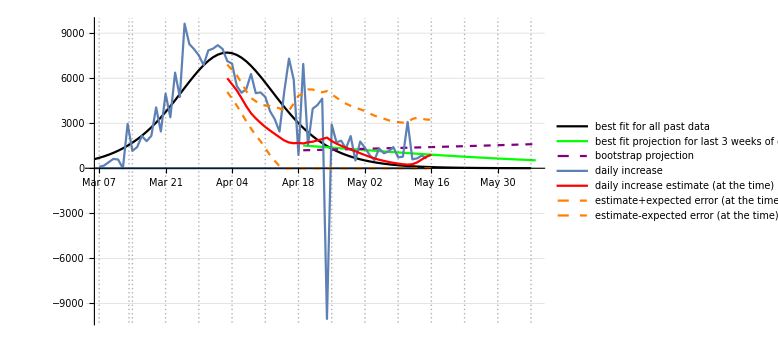

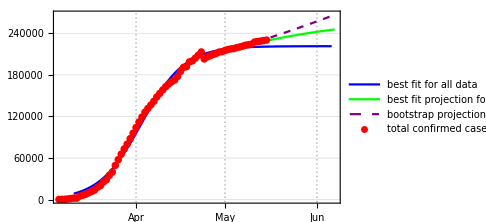

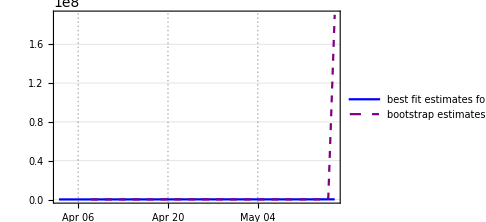

May 15

Spaindate.txt

Spaingraf.png

Spainloggraf.png

Spaindfgraf.png

Spainfinalplot.png

country : Canada

data length : 62

start date : {2020,3,15}

jdp0 : {82564.3,2011.89,0.0945592}

jp20 : {90931.5,3187.96,0.0795016}

backward result : {19758.,271.885,0.236761}

forward result : {90931.5,3187.96,0.0795016}

last tab: {90931.5,3187.96,0.0795016}

backward result : {19758.,271.885,0.236761}

forward result : {90931.5,3187.96,0.0795016}

past errors : {{214.382,302.328,407.177,335.259,245.493,209.407,209.168,256.609,421.26,603.381},320.446}

boot tab : {{45964.5,1055.02,0.134761},{40413.3,945.381,0.143646},{47860.2,1228.25,0.127227},{57820.1,1589.,0.11208},{69248.4,1966.04,0.100292},{78777.9,2323.85,0.0919712},{96797.7,2733.85,0.0835396},{120684.,3157.66,0.0764033},{182039.,3637.78,0.0690106},{230772.,3965.05,0.0651527},{261492.,4221.32,0.0627344},{299529.,4547.98,0.0600505},{209723.,4506.01,0.0616834},{159262.,4447.61,0.0636705},{127431.,4244.93,0.0669304},{112896.,4043.81,0.0697297},{98394.2,3644.62,0.0746826},{91246.,3302.05,0.0788237},{82101.6,2696.91,0.0867844},{85957.5,2949.36,0.0832405},{87589.7,3136.47,0.081158},{87765.,3217.67,0.0804896},{96638.7,4195.26,0.0715204},{102280.,4767.31,0.06718},{107052.,5223.16,0.0640765},{108655.,5479.49,0.0626711},{111805.,5974.59,0.0601418},{111109.,6113.17,0.0597657},{110049.,6202.6,0.0596625},{100472.,5043.63,0.0664235},{95181.1,4127.04,0.0723865},{92363.3,3474.95,0.0770842}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62}

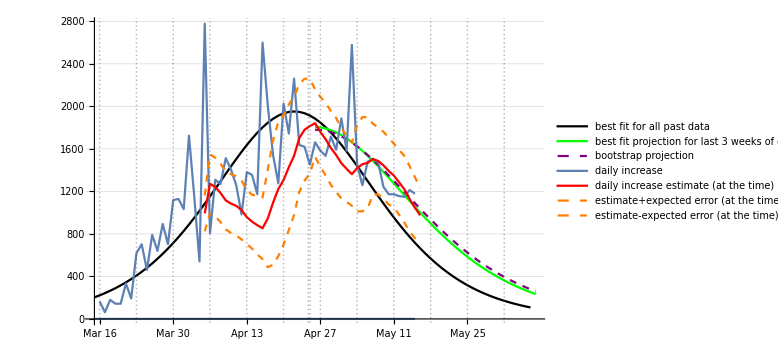

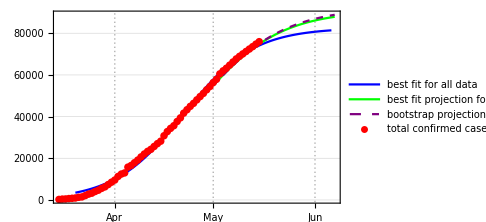

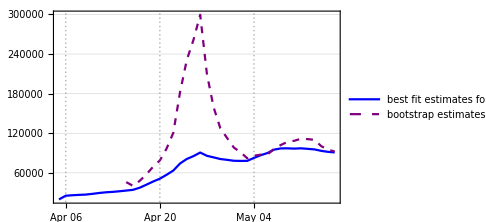

May 15

Canadadate.txt

Canadagraf.png

Canadaloggraf.png

Canadadfgraf.png

Canadafinalplot.png

country : Australia

data length : 67

start date : {2020,3,10}

jdp0 : {6758.57,112.502,0.21606}

jp20 : {4.20599×10^7,5962.44,0.00246865}

backward result : {6180.86,61.6678,0.258699}

forward result : {3.46286×10^7,5962.44,0.00246874}

last tab: {3.46286×10^7,5962.44,0.00246874}

backward result : {6180.86,61.6678,0.258699}

forward result : {3.46286×10^7,5962.44,0.00246874}

past errors : {{1.34346,18.02,20.9803},13.4479}

boot tab : {{6344.63,70.0124,0.249032},{6414.73,74.4046,0.24454},{6470.9,78.4767,0.240699},{6465.91,78.6791,0.240625},{6466.5,79.3324,0.24016},{6486.22,82.1894,0.237935},{6498.56,84.9606,0.235994},{6513.75,89.5754,0.233035},{6552.63,101.063,0.226279},{6591.05,114.737,0.219321},{6617.24,120.224,0.216467},{6637.33,134.975,0.210657},{6658.05,153.162,0.20445},{6679.45,183.264,0.196043},{6693.74,213.067,0.189237},{6717.66,272.51,0.178345},{6731.16,315.53,0.172004},{6750.41,378.656,0.164154},{6752.24,401.374,0.161867},{6779.63,533.885,0.15004},{6796.13,666.2,0.141187},{6819.23,849.87,0.131229},{6834.37,1038.77,0.123242},{6850.9,1192.04,0.117365},{6876.13,1443.34,0.109001},{6920.72,1947.14,0.0953202},{7011.23,2900.98,0.074298},{7139.28,3845.11,0.0552944},{7353.07,4626.56,0.0383062},{7415.69,4842.56,0.0340061},{7482.43,4974.57,0.0309229},{7525.44,5113.68,0.0283346},{8086.79,5493.14,0.0173238},{8485.4,5622.98,0.0135906},{8927.66,5726.06,0.010934},{2.89864×10^7,5936.01,0.00255167},{3.46286×10^7,5951.9,0.00250432}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67}

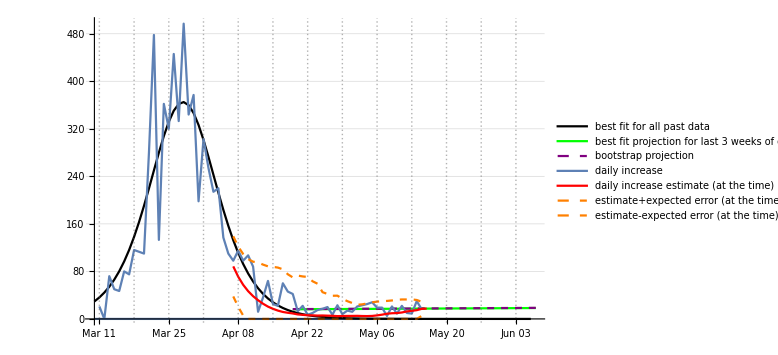

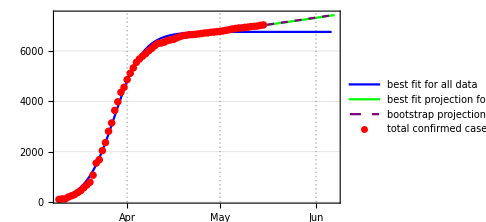

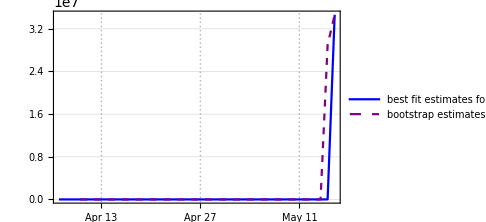

May 15

Australiadate.txt

Australiagraf.png

Australialoggraf.png

Australiadfgraf.png

Australiafinalplot.png

country : New Zealand

data length : 63

start date : {2020,3,14}

jdp0 : {1476.19,18.0121,0.227239}

jp20 : {1508.04,873.38,0.0760065}

backward result : {981.19,4.49853,0.341492}

forward result : {1508.04,873.38,0.0760065}

last tab: {1508.04,873.38,0.0760065}

backward result : {981.19,4.49853,0.341492}

forward result : {1508.04,873.38,0.0760065}

past errors : {{-0.241153,-0.115208,1.11991,2.45067,4.86518,4.353,3.90501,3.51318,4.17051,3.87084},2.78919}

boot tab : {{1833.01,53.1616,0.158085},{1745.34,52.5281,0.161741},{1653.58,49.0838,0.169019},{1584.85,44.396,0.177548},{1536.2,38.8581,0.18697},{1509.47,34.2446,0.194769},{1500.49,32.6958,0.197606},{1488.29,29.0462,0.2039},{1478.53,26.5983,0.208752},{1482.16,31.3381,0.201653},{1481.68,34.8448,0.197617},{1486.04,47.1765,0.185404},{1494.82,73.9462,0.167186},{1492.82,86.0635,0.162189},{1499.51,118.295,0.149442},{1507.24,167.934,0.135325},{1512.91,217.538,0.124841},{1526.04,352.045,0.104276},{1541.97,501.305,0.0868885},{1541.36,548.281,0.0833017},{1538.38,595.871,0.0804977},{1525.29,553.665,0.0871638},{1515.9,524.223,0.0925596},{1510.22,485.594,0.0978167},{1505.99,427.729,0.104363},{1507.1,518.11,0.0971671},{1511.13,670.673,0.0851263},{1514.37,798.974,0.075802},{1511.75,779.767,0.0783427},{1512.5,869.343,0.0727382},{1512.13,923.672,0.0698722},{1517.09,1089.67,0.0568345},{1515.11,1105.19,0.057061}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}

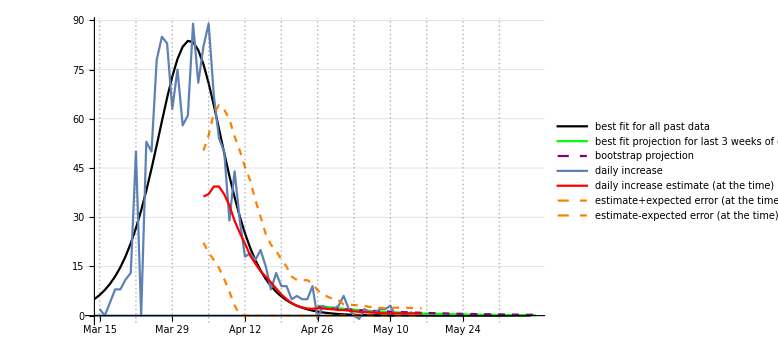

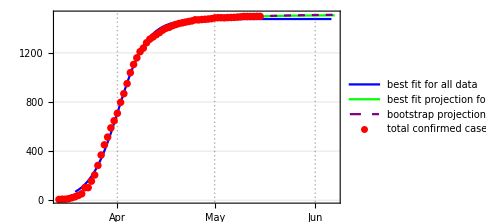

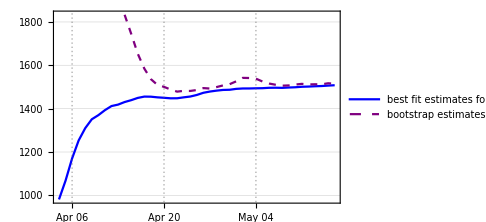

May 15

newzealanddate.txt

newzealandgraf.png

newzealandloggraf.png

newzealanddfgraf.png

newzealandfinalplot.png

country : Croatia

data length : 71

start date : {2020,3,6}

jdp0 : {2147.59,32.8251,0.13921}

jp20 : {2312.3,449.467,0.0639815}

backward result : {1249.12,3.91926,0.255144}

forward result : {2312.3,449.467,0.0639815}

last tab: {2312.3,449.467,0.0639815}

backward result : {1249.12,3.91926,0.255144}

forward result : {2312.3,449.467,0.0639815}

past errors : {{25.4731,28.664,25.2135},26.4502}

boot tab : {{1436.11,6.14465,0.227653},{1427.46,6.12601,0.228018},{1483.03,7.16176,0.219107},{1549.79,8.59725,0.208876},{1647.48,10.9466,0.195544},{1810.36,15.2134,0.177565},{1866.68,17.3217,0.170949},{1970.02,21.0798,0.160901},{2008.1,23.5192,0.155853},{2080.,27.6149,0.148362},{2100.38,30.5155,0.144315},{2154.18,35.5126,0.137846},{2147.,38.5213,0.135222},{2120.19,39.6173,0.134907},{2127.16,42.9707,0.132053},{2097.83,43.2374,0.132655},{2105.06,46.1017,0.130421},{2135.99,51.9069,0.125813},{2176.38,60.4194,0.120006},{2210.66,68.01,0.115478},{2200.23,68.7705,0.115466},{2194.12,70.6698,0.114887},{2178.58,69.4029,0.115947},{2165.98,66.9424,0.117437},{2155.43,60.9536,0.120425},{2152.91,57.6347,0.122033},{2148.42,52.3391,0.124777},{2142.4,47.3249,0.127689},{2139.8,43.6374,0.129887},{2140.69,43.8829,0.129691},{2149.67,49.5264,0.126133},{2158.51,58.4648,0.121538},{2167.5,71.656,0.116097},{2205.02,113.269,0.102709},{2244.75,186.731,0.0884957},{2290.24,288.767,0.075597},{2330.01,400.278,0.0656961},{2367.74,508.817,0.0580129},{2396.43,606.506,0.052347},{2409.42,657.107,0.0497511},{2392.26,656.601,0.0505226}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71}

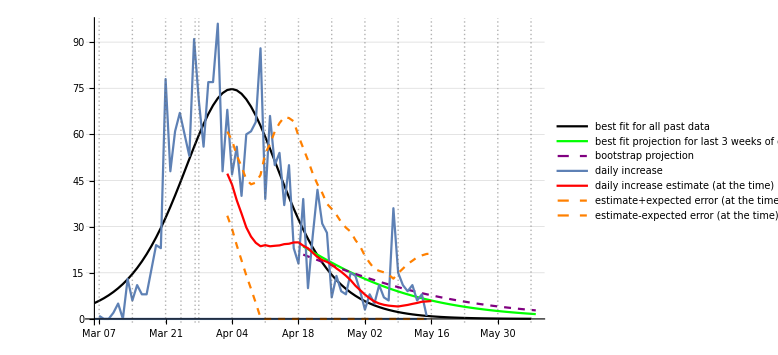

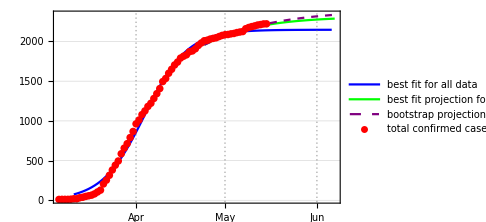

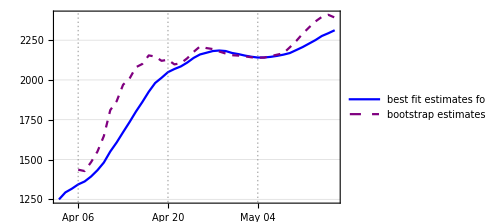

May 15

Croatiadate.txt

Croatiagraf.png

Croatialoggraf.png

Croatiadfgraf.png

Croatiafinalplot.png

country : Czechia

data length : 72

start date : {2020,3,5}

jdp0 : {7967.26,135.03,0.133168}

jp20 : {10088.5,3636.78,0.0299999}

backward result : {2216.85,9.55805,0.303903}

forward result : {10088.5,3636.78,0.0299999}

last tab: {10088.5,3636.78,0.0299999}

backward result : {2216.85,9.55805,0.303903}

forward result : {10088.5,3636.78,0.0299999}

past errors : {{78.1002,106.462,126.308,120.439,126.668,159.819,186.733,218.259,285.26,326.608},173.466}

boot tab : {{9746.37,89.0792,0.147415},{8757.52,93.6428,0.147021},{7322.81,77.909,0.158933},{6079.92,47.0909,0.186442},{6848.02,73.7599,0.16362},{7931.86,112.511,0.142321},{8162.42,128.142,0.136611},{8321.56,143.242,0.131976},{8165.76,146.739,0.131839},{7956.08,149.669,0.132238},{7426.67,128.353,0.140741},{7457.47,143.195,0.137005},{7719.14,184.128,0.127089},{7803.91,208.119,0.122653},{7528.09,173.829,0.130412},{7492.7,175.735,0.130394},{7657.59,229.587,0.120863},{7980.6,340.932,0.106464},{8354.69,521.848,0.0914293},{8663.22,700.572,0.0810726},{9307.2,1016.19,0.0671598},{9728.51,1209.91,0.0604686},{10030.2,1438.86,0.0545394},{10339.,1677.93,0.0492557},{11487.9,2098.19,0.0400292},{12086.1,2318.22,0.0361193},{11819.,2344.34,0.0363221},{10691.9,2147.86,0.0414476},{9429.07,1653.71,0.0535902},{8767.66,1091.38,0.0686605},{8397.53,646.575,0.0848627},{8441.38,725.42,0.0817158},{8512.54,895.862,0.0761402},{8529.72,921.73,0.0753029},{8514.6,887.869,0.0763676},{8588.12,1137.44,0.0700254},{8741.24,1621.04,0.0601674},{9126.97,2495.66,0.045872},{9657.03,3247.17,0.035224},{11071.9,4109.51,0.0231863},{195048.,5153.94,0.00709396},{1.46589×10^8,5136.03,0.00692279}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72}

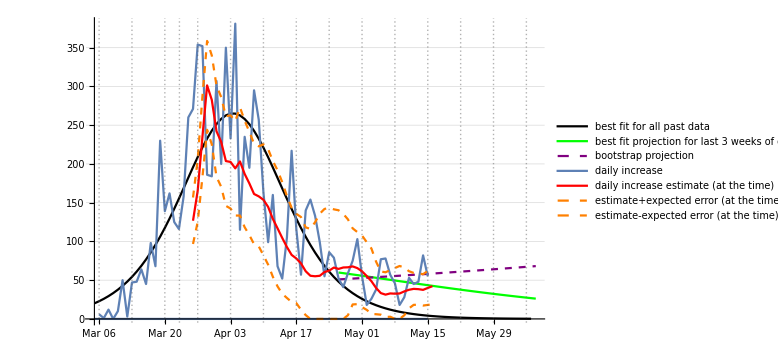

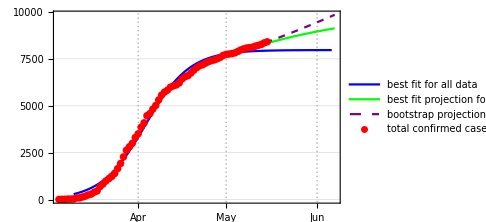

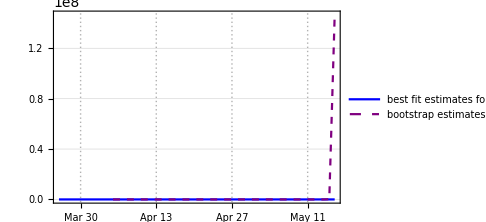

May 15

Czechiadate.txt

Czechiagraf.png

Czechialoggraf.png

Czechiadfgraf.png

Czechiafinalplot.png

country : Sweden

data length : 69

start date : {2020,3,8}

jdp0 : {32365.4,752.543,0.0812114}

jp20 : {40467.7,1806.81,0.0576371}

backward result : {33816.,391.165,0.107741}

forward result : {40467.7,1806.81,0.0576371}

last tab: {40467.7,1806.81,0.0576371}

backward result : {33816.,391.165,0.107741}

forward result : {40467.7,1806.81,0.0576371}

past errors : {{36.7795,280.888,478.14,705.822,695.113,648.096,871.76,1147.01,1474.68,1770.53},810.883}

boot tab : {{14328.6,230.525,0.14094},{15189.8,252.891,0.1354},{16812.4,298.978,0.126058},{18482.6,343.08,0.118537},{18921.5,352.548,0.116978},{18681.,340.621,0.118503},{18698.9,343.557,0.118173},{19793.6,391.331,0.112252},{22360.6,500.522,0.101305},{25768.5,630.977,0.0912165},{30601.6,789.143,0.081737},{35234.9,926.372,0.0752642},{38271.4,1035.56,0.071228},{37837.5,1089.33,0.0700247},{40186.1,1191.01,0.0670223},{42912.6,1301.13,0.0640638},{48101.9,1437.3,0.060466},{47961.8,1484.1,0.0597095},{48083.6,1540.1,0.0588103},{42991.7,1484.04,0.0609178},{38885.9,1401.71,0.0636298},{36574.1,1342.79,0.0656413},{36353.8,1351.17,0.0656313},{37506.4,1420.1,0.0639629},{37944.7,1449.12,0.0633038},{38539.4,1494.78,0.0623435},{37550.9,1453.47,0.0634232},{37142.7,1448.16,0.0637244},{38093.,1559.2,0.0616907},{41026.8,1855.19,0.0567605},{45412.1,2242.55,0.0513302},{50337.3,2615.71,0.0469144}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69}

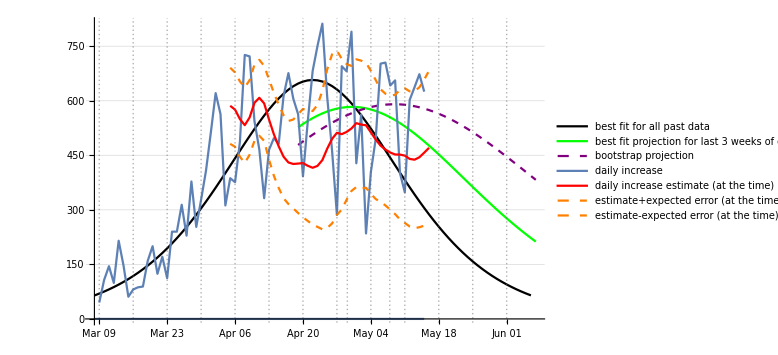

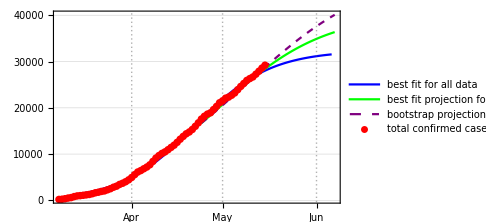

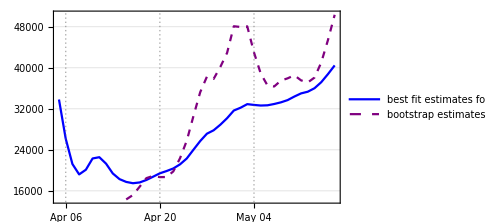

May 15

Swedendate.txt

Swedengraf.png

Swedenloggraf.png

Swedendfgraf.png

Swedenfinalplot.png

country : Greece

data length : 69

start date : {2020,3,8}

jdp0 : {2684.46,133.806,0.118165}

jp20 : {2809.37,182.676,0.0957052}

backward result : {2478.4,89.1455,0.143581}

forward result : {2809.37,182.676,0.0957052}

last tab: {2809.37,182.676,0.0957052}

backward result : {2478.4,89.1455,0.143581}

forward result : {2809.37,182.676,0.0957052}

past errors : {{-20.2973,-19.224,-19.4541,-13.0156,-18.9359,-20.2422,-12.9609,-7.11816,-6.73922,24.1513},-11.3836}

boot tab : {{2352.44,85.4084,0.14789},{2343.2,82.2574,0.149785},{2378.88,87.4267,0.14601},{2379.53,86.5441,0.146415},{2374.13,85.708,0.147053},{2332.45,75.2657,0.15395},{2313.2,68.0001,0.158783},{2460.69,105.336,0.135574},{2480.71,114.594,0.131611},{2574.66,155.517,0.116975},{2663.68,207.482,0.103821},{2751.31,268.599,0.0923139},{2831.38,333.203,0.0829139},{2981.54,446.152,0.0698082},{3254.89,597.533,0.0555793},{3545.4,723.148,0.0460135},{3813.47,804.55,0.0403635},{3858.77,851.617,0.0382303},{3782.99,876.723,0.0378806},{3567.73,866.674,0.0401119},{3425.27,878.147,0.0412799},{3283.76,864.802,0.043684},{3251.32,891.749,0.0432673},{3125.08,838.777,0.0474699},{2993.31,729.365,0.054813},{2911.73,596.623,0.0630439},{2853.22,461.868,0.0721111},{2816.19,344.216,0.0811597},{2810.11,285.828,0.085819},{2815.67,256.654,0.0878688},{2810.39,211.809,0.0924258},{2882.19,377.658,0.0752766}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69}

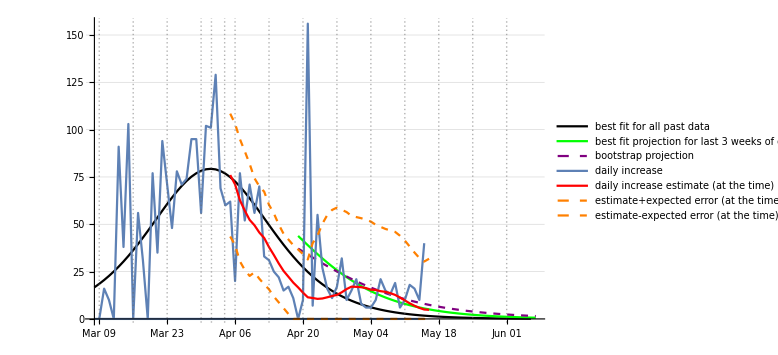

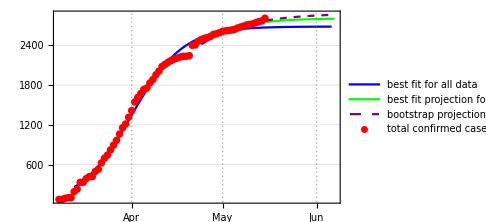

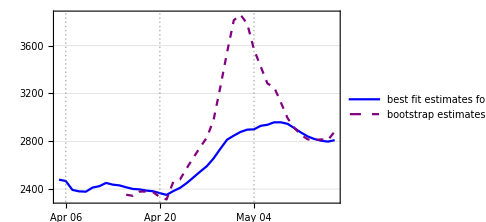

May 15

Greecedate.txt

Greecegraf.png

Greeceloggraf.png

Greecedfgraf.png

Greecefinalplot.png

country : Japan

data length : 57

start date : {2020,3,20}

jdp0 : {16343.7,456.606,0.132137}

jp20 : {16571.4,799.394,0.114923}

backward result : {61680.7,682.989,0.0970644}

forward result : {16571.4,799.394,0.114923}

last tab: {16571.4,799.394,0.114923}

backward result : {61680.7,682.989,0.0970644}

forward result : {16571.4,799.394,0.114923}

past errors : {{186.288,204.558,257.504,274.104,348.442,388.702,424.159,476.169},319.991}

boot tab : {{13315.9,224.523,0.172372},{12884.9,183.951,0.183025},{12913.8,169.381,0.18627},{13895.7,210.611,0.172145},{14183.,221.253,0.168669},{14778.9,252.027,0.160776},{15213.8,273.627,0.155685},{15185.2,264.216,0.157101},{15204.2,253.168,0.158499},{15385.7,269.733,0.155293},{15572.8,286.889,0.152121},{15510.1,281.065,0.153143},{15673.4,313.075,0.148617},{16104.5,415.583,0.136944},{16354.4,485.623,0.130597},{16549.8,566.312,0.124749},{16728.6,644.714,0.119783},{16719.7,656.461,0.119278},{16854.1,778.881,0.113478},{16953.4,944.556,0.107381},{17125.5,1234.12,0.0988339},{17087.5,1245.1,0.0988276}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

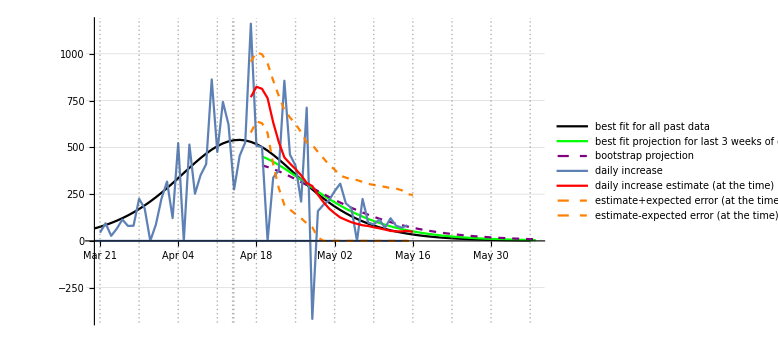

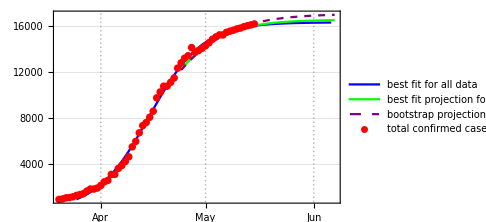

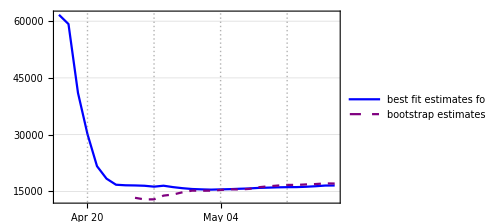

May 15

Japandate.txt

Japangraf.png

Japanloggraf.png

Japandfgraf.png

Japanfinalplot.png

country : Denmark

data length : 59

start date : {2020,3,18}

jdp0 : {11100.1,1125.64,0.0912458}

jp20 : {12656.7,2243.57,0.0585822}

backward result : {9622.11,847.804,0.116597}

forward result : {12656.7,2243.57,0.0585822}

last tab: {12656.7,2243.57,0.0585822}

backward result : {9622.11,847.804,0.116597}

forward result : {12656.7,2243.57,0.0585822}

past errors : {{9.63543,37.4959,59.2075,50.7519,55.1004,37.2148,17.048,-1.4547,-46.355,-55.721},16.2923}

boot tab : {{8789.2,690.271,0.132732},{9408.77,861.385,0.115934},{9904.5,1019.76,0.104163},{10433.3,1208.42,0.0930967},{11116.9,1440.04,0.0818724},{12051.9,1723.91,0.0705372},{13311.5,2038.43,0.0600674},{14942.3,2343.1,0.0513308},{16294.8,2588.,0.0456477},{18136.9,2839.26,0.0403361},{21170.9,3096.81,0.035147},{23245.4,3265.43,0.0323379},{22570.4,3327.2,0.0320358},{21830.8,3367.96,0.0320182},{20732.4,3388.28,0.0324607},{18584.,3330.68,0.0346045},{16820.3,3229.62,0.0374526},{15384.5,3089.32,0.0410211},{14363.4,2912.09,0.0450017},{13624.2,2711.42,0.0492465},{12879.6,2385.73,0.0558036},{12512.6,2138.64,0.060687}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59}

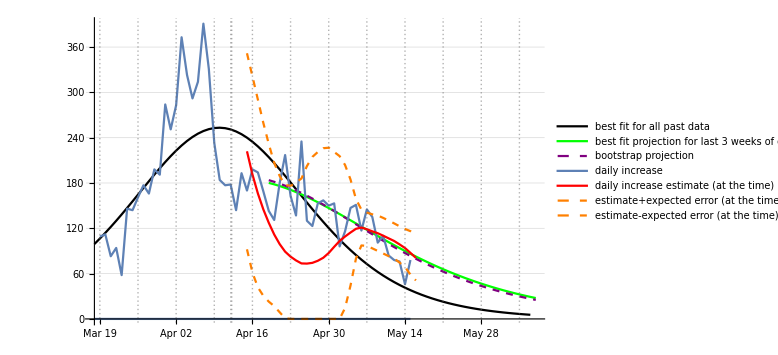

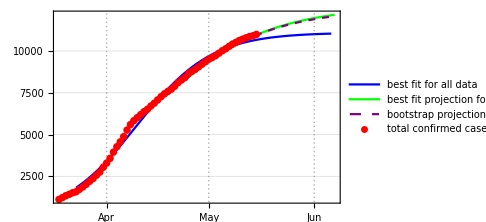

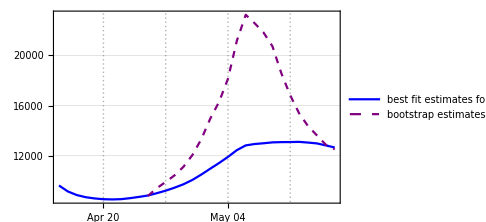

May 15

Denmarkdate.txt

Denmarkgraf.png

Denmarkloggraf.png

Denmarkdfgraf.png

Denmarkfinalplot.png

country : Russia

data length : 56

start date : {2020,3,21}

jdp0 : {379965.,1459.63,0.11323}

jp20 : {436199.,2200.45,0.10199}

backward result : {40899.,291.658,0.19182}

forward result : {436199.,2200.45,0.10199}

last tab: {436199.,2200.45,0.10199}

backward result : {40899.,291.658,0.19182}

forward result : {436199.,2200.45,0.10199}

past errors : {{3796.35,5852.77,7421.43,9208.38,11344.2,14327.8,16803.3,18696.4,20857.5,23991.7},13230.}

boot tab : {{339753.,540.719,0.148964},{272232.,541.224,0.149824},{216291.,537.8,0.151313},{166931.,488.092,0.156903},{148516.,426.755,0.163075},{133704.,340.318,0.172608},{134487.,325.5,0.174075},{134147.,304.939,0.176344},{130117.,251.508,0.183418},{113530.,111.805,0.213888},{132929.,236.39,0.184824},{153795.,406.755,0.164158},{195097.,798.069,0.139122},{277844.,1473.14,0.116604},{402294.,2168.37,0.102661},{589601.,2844.32,0.0932146},{866125.,3450.89,0.0867415},{1.33778×10^6,4007.18,0.0818926},{1.85067×10^6,4459.32,0.0787167},{2.04861×10^6,4727.18,0.077201},{1.71019×10^6,4795.62,0.0771761},{1.4578×10^6,4860.79,0.0772081},{1.12311×10^6,4809.04,0.078158},{820690.,4491.48,0.0809398},{621510.,3848.,0.0860709},{509416.,3038.66,0.0930349}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

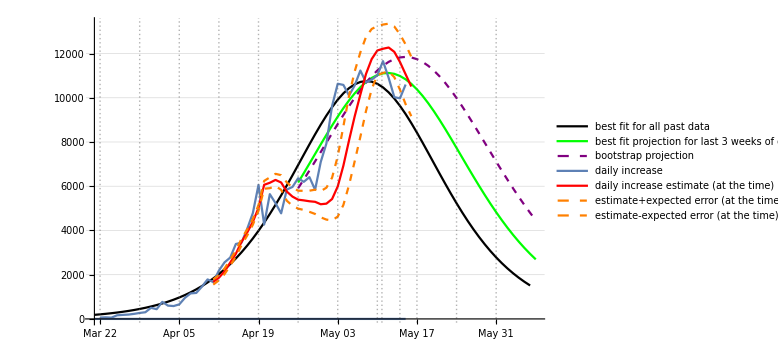

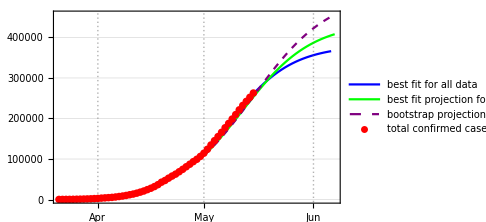

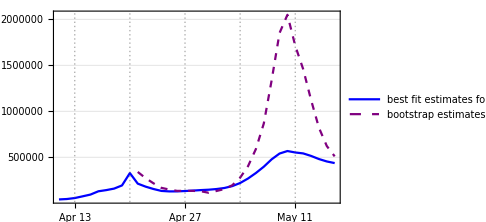

May 15

Russiadate.txt

Russiagraf.png

Russialoggraf.png

Russiadfgraf.png

Russiafinalplot.png

country : United Kingdom

data length : 70

start date : {2020,3,7}

jdp0 : {248808.,2845.53,0.0985659}

jp20 : {306556.,10026.2,0.0663728}

backward result : {109233.,204.099,0.209633}

forward result : {306556.,10026.2,0.0663728}

last tab: {306556.,10026.2,0.0663728}

backward result : {109233.,204.099,0.209633}

forward result : {306556.,10026.2,0.0663728}

past errors : {{2199.79,3726.89,4408.69,4459.06,4665.05,4959.94,4912.21,4831.66,5094.39,5597.92},4485.56}

boot tab : {{83241.9,195.501,0.211712},{78715.9,169.211,0.218966},{104119.,386.441,0.179579},{124173.,562.919,0.162089},{161690.,722.568,0.149431},{167872.,807.496,0.145055},{167177.,860.08,0.143001},{161292.,887.738,0.142526},{173543.,1053.12,0.13579},{164724.,1037.13,0.137269},{173159.,1212.29,0.131495},{191688.,1498.9,0.123273},{201406.,1708.79,0.1186},{216532.,2016.16,0.112684},{204744.,2024.87,0.113565},{199855.,2112.68,0.112913},{199191.,2256.34,0.111236},{206738.,2631.07,0.106331},{218142.,3158.27,0.100419},{233208.,3921.28,0.0935452},{245292.,4596.52,0.0886055},{256027.,5373.87,0.0839984},{266253.,6354.42,0.0792965},{271707.,7244.,0.0758797},{303860.,9479.33,0.0678445},{342853.,11586.,0.0616172},{384735.,13746.,0.0564606},{420258.,15595.3,0.0528094},{442573.,17236.6,0.0501939},{452556.,18487.3,0.0485367},{557306.,21804.8,0.0435262},{777099.,25866.8,0.0383125},{998570.,28707.5,0.0353624},{979455.,29777.3,0.0347381},{657178.,27447.,0.0380413},{507881.,24665.4,0.0419025},{418843.,21208.1,0.0467807},{370329.,17956.5,0.0516757},{343410.,15264.,0.0560629},{325565.,12751.1,0.0604977}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70}

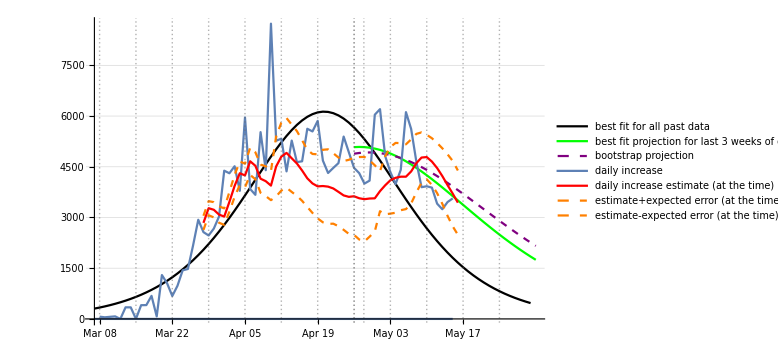

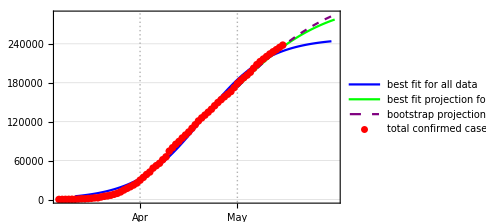

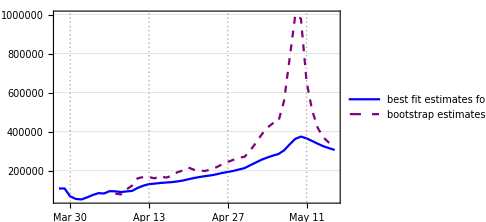

May 15

ukdate.txt

ukgraf.png

ukloggraf.png

ukdfgraf.png

ukfinalplot.png

country : Hungary

data length : 59

start date : {2020,3,18}

jdp0 : {3521.54,114.749,0.108744}

jp20 : {3602.74,139.19,0.101409}

backward result : {3559.03,90.161,0.121211}

forward result : {3602.74,139.19,0.101409}

last tab: {3602.74,139.19,0.101409}

backward result : {3559.03,90.161,0.121211}

forward result : {3602.74,139.19,0.101409}

past errors : {{-4.55343,-6.713,-16.9199,-17.3113,-0.030587,-9.22507,-8.04315,-5.63253,9.86144,25.2972},-3.32703}

boot tab : {{3044.96,96.0426,0.121224},{3174.56,105.671,0.115803},{3330.85,114.155,0.111136},{3420.45,118.838,0.108739},{3501.07,123.761,0.106464},{3623.3,132.405,0.102939},{3679.16,137.508,0.101118},{3775.03,146.665,0.0981112},{3908.22,160.356,0.0940671},{3912.03,166.408,0.0928646},{3757.9,161.808,0.0952574},{3780.51,174.733,0.092735},{3896.66,202.083,0.0872517},{3974.93,229.137,0.0828742},{3934.02,228.179,0.0834191},{3864.53,215.895,0.0857395},{3863.12,211.694,0.0862594},{3774.56,190.799,0.0902303},{3708.16,174.195,0.0936521},{3659.9,161.287,0.0964908},{3643.3,157.443,0.0974362},{3639.91,154.15,0.0980334}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59}

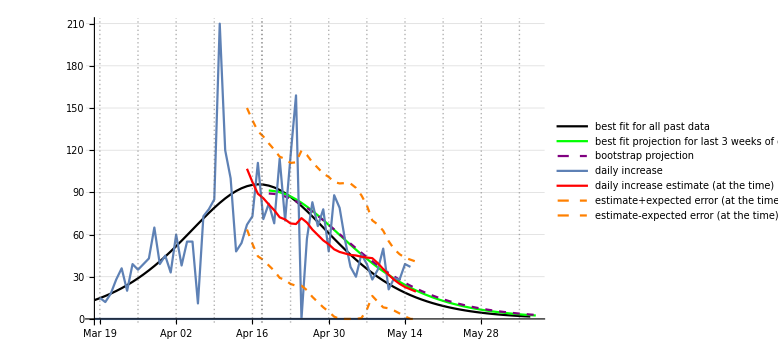

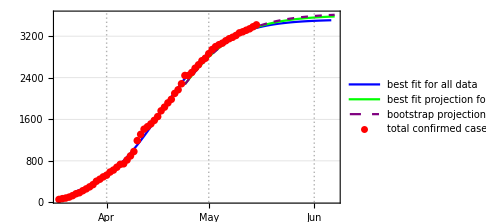

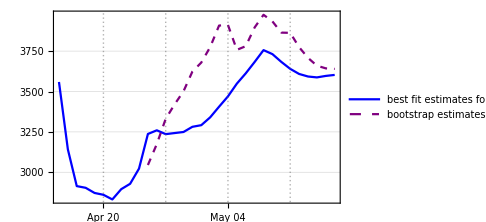

May 15

Hungarydate.txt

Hungarygraf.png

Hungaryloggraf.png

Hungarydfgraf.png

Hungaryfinalplot.png

country : France

data length : 72

start date : {2020,3,5}

jdp0 : {178205.,1576.44,0.136603}

jp20 : {190266.,45868.7,0.0552612}

backward result : {113682.,799.423,0.176917}

forward result : {190266.,45868.7,0.0552612}

last tab: {190266.,45868.7,0.0552612}

backward result : {113682.,799.423,0.176917}

forward result : {190266.,45868.7,0.0552612}

past errors : {{6133.37,6746.99,7966.43,8494.58,8764.95,9184.52,9959.68,9773.13,10565.8,11187.9},8877.74}

boot tab : {{106792.,853.645,0.175194},{201833.,2616.02,0.11642},{294439.,3813.15,0.0985153},{440984.,4843.79,0.0874727},{535015.,5397.82,0.0829994},{887709.,5847.48,0.0788206},{824902.,6165.43,0.0774565},{575923.,6119.55,0.0791565},{489370.,6013.28,0.0807104},{410677.,5810.09,0.083058},{364632.,5587.52,0.0853636},{247538.,4071.31,0.099892},{195876.,2259.24,0.12284},{172293.,1176.87,0.14666},{164753.,788.875,0.160283},{152737.,373.292,0.186111},{152267.,292.094,0.193025},{156296.,279.592,0.191939},{154939.,173.258,0.20524},{156413.,131.991,0.211361},{157158.,85.9456,0.221847},{160019.,67.6592,0.225927},{161798.,49.6329,0.232403},{163385.,35.6734,0.239374},{165048.,27.9327,0.244008},{168297.,43.265,0.230544},{169676.,60.186,0.221366},{171947.,219.205,0.188979},{176881.,3067.55,0.125106},{180221.,7034.43,0.104002},{186462.,20712.1,0.075657},{200100.,51878.5,0.0470492},{236103.,87513.8,0.0246311},{286101.,98977.2,0.0169582},{431142.,107688.,0.0111359}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72}

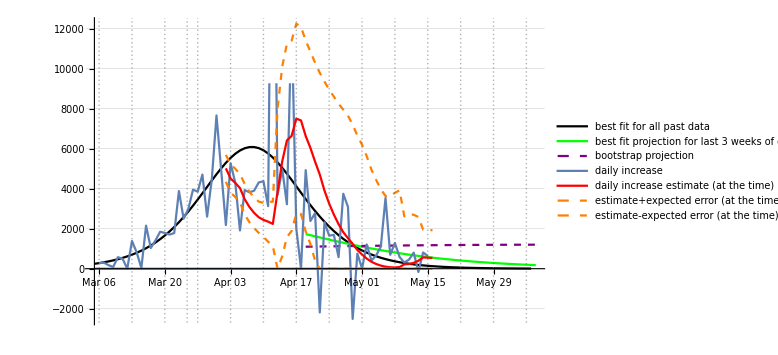

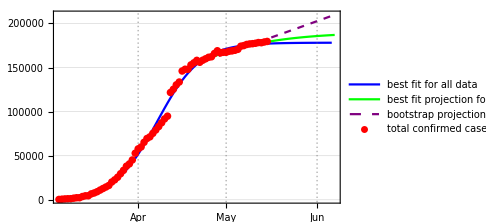

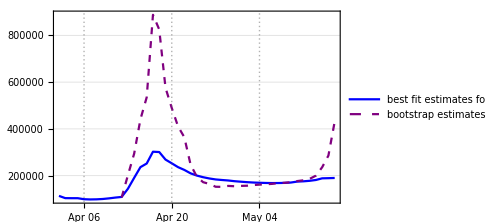

May 15

Francedate.txt

Francegraf.png

Franceloggraf.png

Francedfgraf.png

Francefinalplot.png

country : Singapore

data length : 46

start date : {2020,3,31}

jdp0 : {27926.3,638.928,0.132217}

jp20 : {31417.5,1282.51,0.103309}

backward result : {25787.1,368.544,0.161986}

forward result : {31417.5,1282.51,0.103309}

last tab: {31417.5,1282.51,0.103309}

backward result : {25787.1,368.544,0.161986}

forward result : {31417.5,1282.51,0.103309}

past errors : {{1429.29,2030.66,2489.13,3052.32,3681.06},2536.49}

boot tab : {{18609.7,185.163,0.206979},{19843.4,225.079,0.194109},{20798.2,259.355,0.184972},{21901.1,305.638,0.174815},{22991.7,359.902,0.165125},{24335.4,433.925,0.154339},{25866.,529.876,0.143264},{27652.9,655.403,0.131943},{30184.6,842.18,0.118987},{31527.8,979.632,0.1119},{34393.9,1232.6,0.100938},{37062.2,1502.7,0.0920415},{40493.3,1831.63,0.0832682},{44942.5,2233.67,0.0746694}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46}

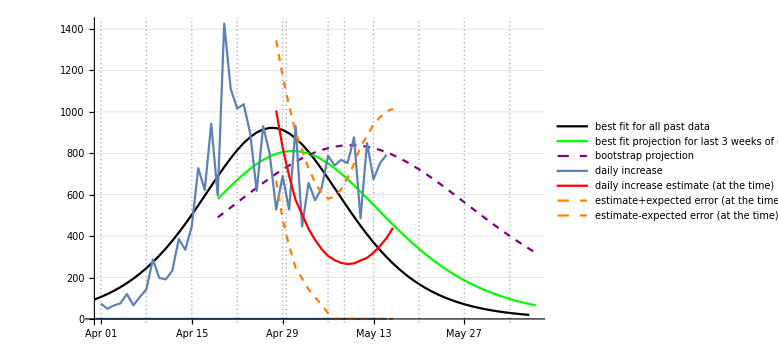

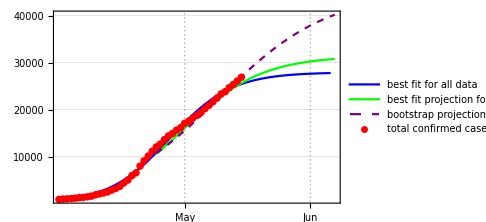

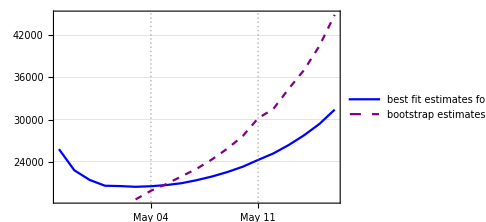

May 15

Singaporedate.txt

Singaporegraf.png

Singaporeloggraf.png

Singaporedfgraf.png

Singaporefinalplot.png

country : Serbia

data length : 61

start date : {2020,3,16}

jdp0 : {10466.7,130.619,0.13507}

jp20 : {10676.8,150.046,0.127811}

backward result : {7513.09,63.8328,0.174541}

forward result : {10676.8,150.046,0.127811}

last tab: {10676.8,150.046,0.127811}

backward result : {7513.09,63.8328,0.174541}

forward result : {10676.8,150.046,0.127811}

past errors : {{-22.7926,-77.4562,-84.9302,-89.7833,-175.583,-109.89,-114.25,-127.187,-107.206,-96.7835},-100.586}

boot tab : {{7872.36,80.0471,0.161469},{8091.22,79.0902,0.161508},{9878.52,113.688,0.141968},{12041.2,151.828,0.126886},{14143.7,180.709,0.117967},{15295.2,199.488,0.113426},{15208.3,210.216,0.111714},{14947.,217.864,0.110804},{13109.8,207.562,0.114692},{11375.5,171.835,0.124269},{10419.3,140.048,0.133769},{9453.12,93.044,0.15102},{8957.86,62.083,0.166787},{9034.08,59.4092,0.167549},{9240.84,65.0643,0.163211},{9614.06,85.7511,0.152371},{9617.75,86.8604,0.151922},{10357.2,165.735,0.12884},{10990.4,276.709,0.111421},{11680.,429.866,0.0965817},{12159.9,574.659,0.0871627},{12538.9,721.804,0.0799786},{12506.4,781.144,0.0780925},{12473.3,827.699,0.076768},{12329.7,843.689,0.0768584},{11613.1,625.672,0.0875526},{11620.,630.033,0.0873465},{11171.3,413.669,0.100178},{10798.4,209.091,0.119019},{10677.7,147.129,0.128216},{10618.8,120.762,0.133348}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61}

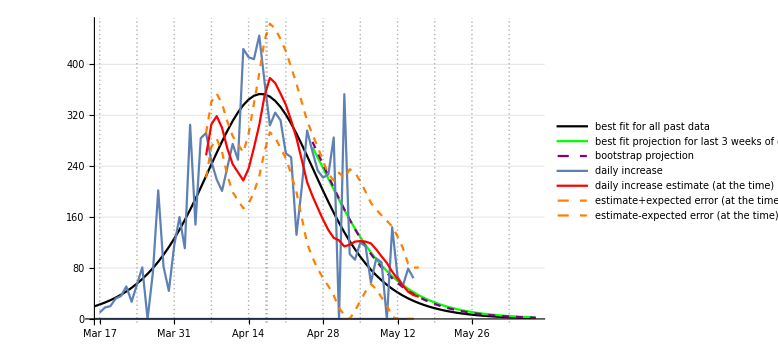

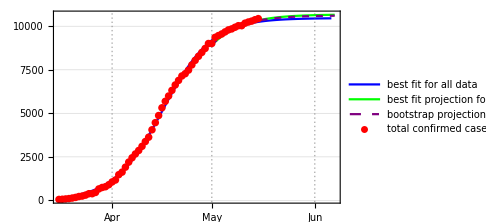

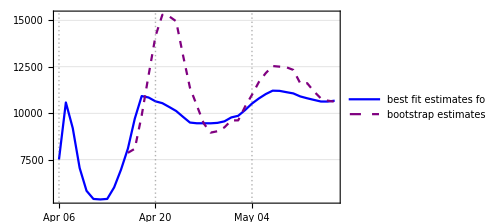

May 15

Serbiadate.txt

Serbiagraf.png

Serbialoggraf.png

Serbiadfgraf.png

Serbiafinalplot.png

country : Poland

data length : 64

start date : {2020,3,13}

jdp0 : {18506.9,505.221,0.0921933}

jp20 : {102779.,3813.48,0.0266427}

backward result : {5109.3,89.9793,0.203261}

forward result : {102779.,3813.48,0.0266427}

last tab: {102779.,3813.48,0.0266427}

backward result : {5109.3,89.9793,0.203261}

forward result : {102779.,3813.48,0.0266427}

past errors : {{103.7,417.596,425.354,567.193,705.305},443.83}

boot tab : {{13272.1,157.154,0.150388},{10722.3,148.097,0.156827},{10669.8,150.507,0.15615},{9826.37,142.586,0.160728},{10163.3,149.628,0.157591},{9836.11,145.434,0.159836},{9516.67,138.606,0.163089},{9375.17,133.946,0.165148},{9672.35,143.474,0.160997},{9894.68,152.667,0.157488},{10817.8,194.407,0.144308},{11841.3,244.185,0.132299},{14455.5,358.338,0.112344},{16097.5,439.7,0.102625},{17091.2,505.159,0.0966589},{17773.8,572.902,0.0917365},{18514.2,644.031,0.0871774},{18404.3,681.853,0.0854911},{19190.5,769.879,0.0809218},{19777.7,837.104,0.0778199},{19690.,875.859,0.0766152},{19572.9,897.994,0.0760464},{20807.9,1002.7,0.0716649},{19467.3,935.077,0.0750684},{18306.5,837.923,0.0796605},{17656.8,750.901,0.0836719},{17660.7,734.868,0.0842022},{17651.2,731.691,0.0843175},{19181.1,976.567,0.0743145},{21028.9,1264.64,0.0653958},{24315.,1697.2,0.0551105},{28845.3,2123.16,0.0470493},{33457.3,2465.88,0.0418017},{33904.3,2539.89,0.0409908},{34224.9,2612.63,0.0402658},{96048.7,3534.91,0.0282625},{240750.,3862.28,0.0251233},{2.74584×10^8,4004.15,0.0236288},{2.27979×10^7,3969.97,0.0238096}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

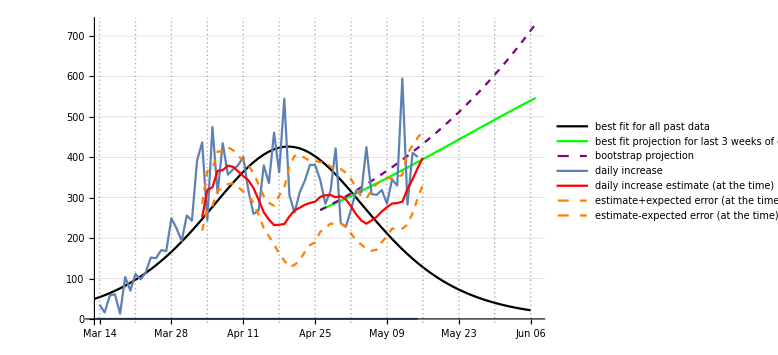

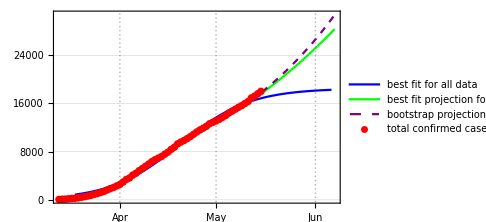

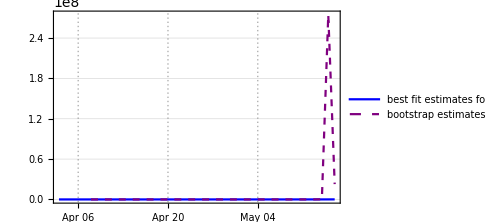

May 15

Polanddate.txt

Polandgraf.png

Polandloggraf.png

Polanddfgraf.png

Polandfinalplot.png

{136.33467,Null}

```mathematica
countrydateplotlist={};
Timing[
For[cit=1,cit≤Length[countryparameters],cit++,
countrynames=Transpose[countryparameters][[1]];
currentnamme=countrynames[[cit]];
{currentnamme,ctrunc,jdp0,jlag,jprojtime,jbootlag,jplotdrop}=countryparameters[[cit]];
Print["country : ",currentnamme];
countinds=Flatten[Position[countriescsv,currentnamme]];
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}];

truncdatesandata=Select[datesanddata,#[[2]]>ctrunc&];
justdata=Transpose[truncdatesandata][[2]];
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]];
Print["data length : ",Length[justdata]];
Print["start date : ",jstartdate];

{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime];
Print["jdp0 : ",jdp0];
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,jlag,justtime,{1,0}];
Print["jp20 : ",jp20];

(*update jdp0*)
countryparameters[[cit,3]]=jdp0;

{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,jbootabc}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,jlag,jprojtime,5,jbootlag,wpopulations[[cit]]];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]-1];
Print[jgraf];
Print[jloggraf];
Print[jfinal];

(*jdatestring=reldatetostring[cpstartdate,timecpert[[-1]]];*)

Print[jdatestring];

If[jp20[[1]]10^5/wpopulations[[cit]]>grafthreshhold,
morecountrynames=AppendTo[morecountrynames,currentnamme],
lesscountrynames=AppendTo[lesscountrynames,currentnamme]
];

(*new zealand string exception*)
If[currentnamme==="New Zealand",currentnamme="newzealand"];
(*uk  string exception*)
If[currentnamme==="United Kingdom",currentnamme="uk"];


datefilename=currentnamme<>"date.txt";
Print[datefilename];
Export[datefilename,jdatestring];
graffilename=currentnamme<>"graf.png";
Export[graffilename,jgraf];
Print[graffilename];
loggraffilename=currentnamme<>"loggraf.png";
Export[loggraffilename,jloggraf];
Print[loggraffilename];
dfgraffilename=currentnamme<>"dfgraf.png";
Export[dfgraffilename,jdfpplot];
Print[dfgraffilename];
finalgraffilename=currentnamme<>"finalplot.png";
Export[finalgraffilename,jfinal];
Print[finalgraffilename];

drcases=Transpose[datesanddata][[2]];
drcases=drcases/wpopulations[[cit]];
datesanddata=Transpose[{Transpose[datesanddata][[1]],drcases}];
countrydateplotlist=AppendTo[countrydateplotlist,datesanddata];
]
]
```

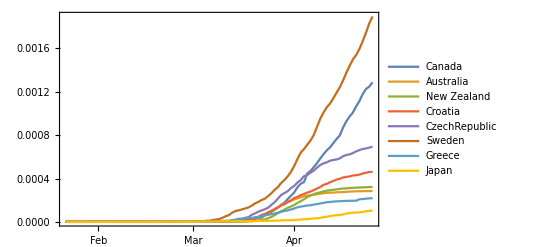

```mathematica
DateListPlot[countrydateplotlist,PlotLegends->wolfcountrynames,PlotRange->All]
```

```mathematica
allcountrynames=Join[fwcountrynames,wolfcountrynames]
%//Length
Length[countrybootabcs]
```

{Slovenia,Italy,Austria,Germany,USA,Canada,Australia,New Zealand,Croatia,CzechRepublic,Singapore,Japan}

12

12

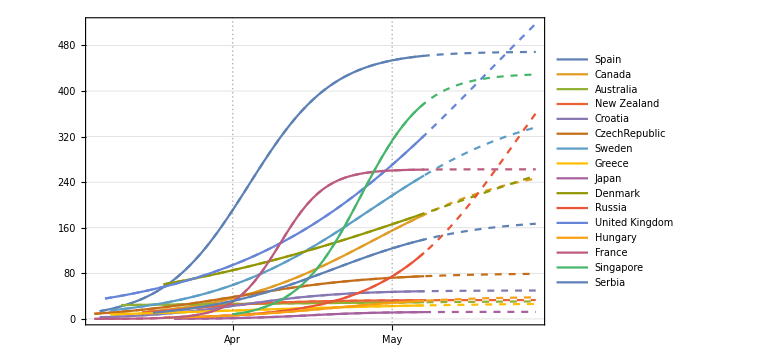

```mathematica
projfwcountryplot=DateListPlot[countrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,countrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->wolfcountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

```mathematica
countrybootabcs//Length
morecountrybootabcs//Length
lesscountrybootabcs//Length
morecountrynames
lesscountrynames
```

17

9

8

{Spain,Canada,Sweden,Denmark,Russia,United Kingdom,France,Singapore,Serbia}

{Australia,New Zealand,Croatia,Czechia,Greece,Japan,Hungary,Poland}

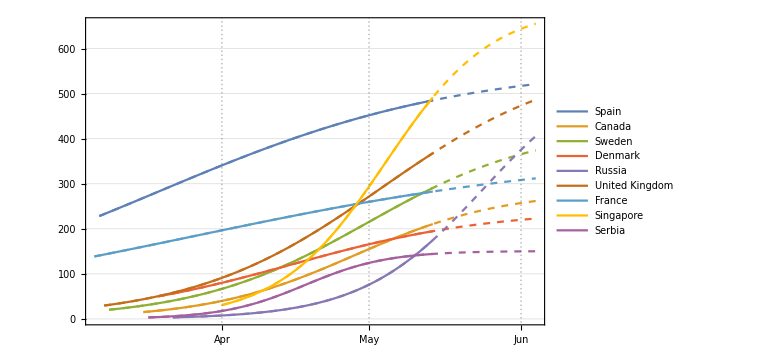

```mathematica
projfwcountryplot=DateListPlot[morecountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,morecountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->morecountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["moremscprojplots.png",mscprojplots]
```

moremscprojplots.png

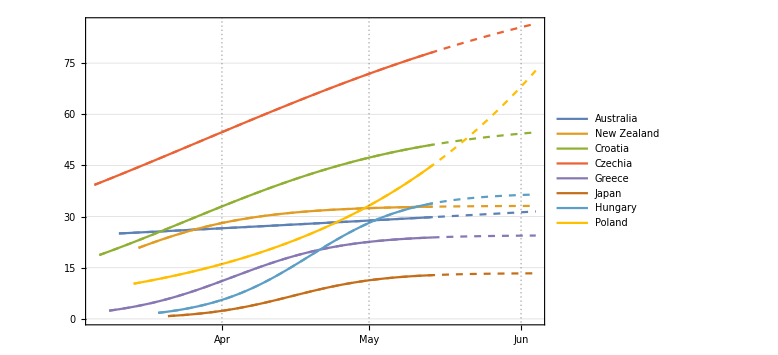

```mathematica
projfwcountryplot=DateListPlot[lesscountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,lesscountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->lesscountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["lessmscprojplots.png",mscprojplots]
```

lessmscprojplots.png

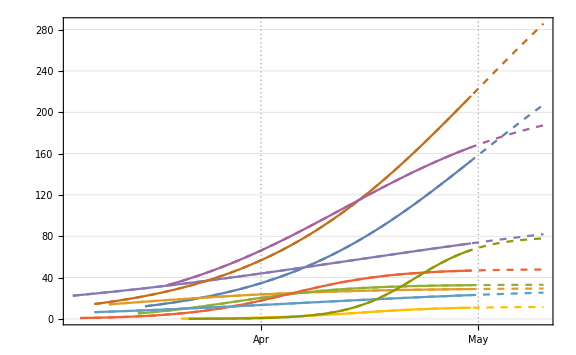
```mathematica
29.4.
-Graphics-
```

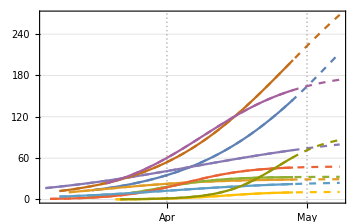
```mathematica
28.4.
-Graphics-
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

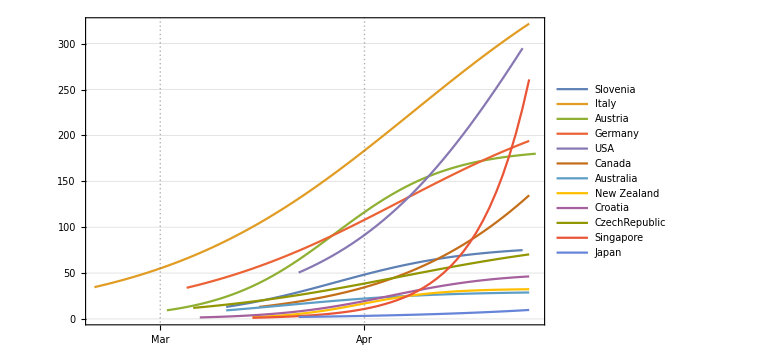

```mathematica
DateListPlot[countrybootabcs,PlotRange->All,PlotLegends->allcountrynames,ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
ColorData
```

```mathematica
countinds=Flatten[Position[countriescsv,"Poland"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{185}

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},0},{{2020,1,27},0},{{2020,1,28},0},{{2020,1,29},0},{{2020,1,30},0},{{2020,1,31},0},{{2020,2,1},0},{{2020,2,2},0},{{2020,2,3},0},{{2020,2,4},0},{{2020,2,5},0},{{2020,2,6},0},{{2020,2,7},0},{{2020,2,8},0},{{2020,2,9},0},{{2020,2,10},0},{{2020,2,11},0},{{2020,2,12},0},{{2020,2,13},0},{{2020,2,14},0},{{2020,2,15},0},{{2020,2,16},0},{{2020,2,17},0},{{2020,2,18},0},{{2020,2,19},0},{{2020,2,20},0},{{2020,2,21},0},{{2020,2,22},0},{{2020,2,23},0},{{2020,2,24},0},{{2020,2,25},0},{{2020,2,26},0},{{2020,2,27},0},{{2020,2,28},0},{{2020,2,29},0},{{2020,3,1},0},{{2020,3,2},0},{{2020,3,3},0},{{2020,3,4},1},{{2020,3,5},1},{{2020,3,6},5},{{2020,3,7},5},{{2020,3,8},11},{{2020,3,9},16},{{2020,3,10},22},{{2020,3,11},31},{{2020,3,12},49},{{2020,3,13},68},{{2020,3,14},103},{{2020,3,15},119},{{2020,3,16},177},{{2020,3,17},238},{{2020,3,18},251},{{2020,3,19},355},{{2020,3,20},425},{{2020,3,21},536},{{2020,3,22},634},{{2020,3,23},749},{{2020,3,24},901},{{2020,3,25},1051},{{2020,3,26},1221},{{2020,3,27},1389},{{2020,3,28},1638},{{2020,3,29},1862},{{2020,3,30},2055},{{2020,3,31},2311},{{2020,4,1},2554},{{2020,4,2},2946},{{2020,4,3},3383},{{2020,4,4},3627},{{2020,4,5},4102},{{2020,4,6},4413},{{2020,4,7},4848},{{2020,4,8},5205},{{2020,4,9},5575},{{2020,4,10},5955},{{2020,4,11},6356},{{2020,4,12},6674},{{2020,4,13},6934},{{2020,4,14},7202},{{2020,4,15},7582},{{2020,4,16},7918},{{2020,4,17},8379},{{2020,4,18},8742},{{2020,4,19},9287},{{2020,4,20},9593},{{2020,4,21},9856},{{2020,4,22},10169},{{2020,4,23},10511},{{2020,4,24},10892},{{2020,4,25},11273},{{2020,4,26},11617},{{2020,4,27},11902},{{2020,4,28},12218},{{2020,4,29},12640},{{2020,4,30},12877},{{2020,5,1},13105},{{2020,5,2},13375},{{2020,5,3},13693},{{2020,5,4},14006},{{2020,5,5},14431},{{2020,5,6},14740},{{2020,5,7},15047},{{2020,5,8},15366}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>50&]
%//Length
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]]
```

{{{2020,3,13},68},{{2020,3,14},103},{{2020,3,15},119},{{2020,3,16},177},{{2020,3,17},238},{{2020,3,18},251},{{2020,3,19},355},{{2020,3,20},425},{{2020,3,21},536},{{2020,3,22},634},{{2020,3,23},749},{{2020,3,24},901},{{2020,3,25},1051},{{2020,3,26},1221},{{2020,3,27},1389},{{2020,3,28},1638},{{2020,3,29},1862},{{2020,3,30},2055},{{2020,3,31},2311},{{2020,4,1},2554},{{2020,4,2},2946},{{2020,4,3},3383},{{2020,4,4},3627},{{2020,4,5},4102},{{2020,4,6},4413},{{2020,4,7},4848},{{2020,4,8},5205},{{2020,4,9},5575},{{2020,4,10},5955},{{2020,4,11},6356},{{2020,4,12},6674},{{2020,4,13},6934},{{2020,4,14},7202},{{2020,4,15},7582},{{2020,4,16},7918},{{2020,4,17},8379},{{2020,4,18},8742},{{2020,4,19},9287},{{2020,4,20},9593},{{2020,4,21},9856},{{2020,4,22},10169},{{2020,4,23},10511},{{2020,4,24},10892},{{2020,4,25},11273},{{2020,4,26},11617},{{2020,4,27},11902},{{2020,4,28},12218},{{2020,4,29},12640},{{2020,4,30},12877},{{2020,5,1},13105},{{2020,5,2},13375},{{2020,5,3},13693},{{2020,5,4},14006},{{2020,5,5},14431},{{2020,5,6},14740},{{2020,5,7},15047},{{2020,5,8},15366}}

57

{68,103,119,177,238,251,355,425,536,634,749,901,1051,1221,1389,1638,1862,2055,2311,2554,2946,3383,3627,4102,4413,4848,5205,5575,5955,6356,6674,6934,7202,7582,7918,8379,8742,9287,9593,9856,10169,10511,10892,11273,11617,11902,12218,12640,12877,13105,13375,13693,14006,14431,14740,15047,15366}

{2020,3,13}

```mathematica
jdp0={Max[justdata]1.5,150,0.12}
```

{23049.,150,0.12}

```mathematica
jdp0={2.835279843883035*^8,64.38918662693713,0.1259411788554341}
```

{2.83528×10^8,64.3892,0.125941}

```mathematica
jdp0={1.1513551375078703*^6,30102.77946079763,0.1242005827138709}
```

{1.15136×10^6,30102.8,0.124201}

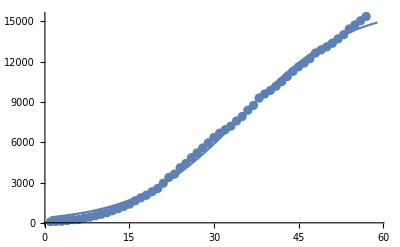

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{16098.4,370.628,0.106508},14,2.69826×10^-8,57}

{19509.6,978.105,0.0737384}

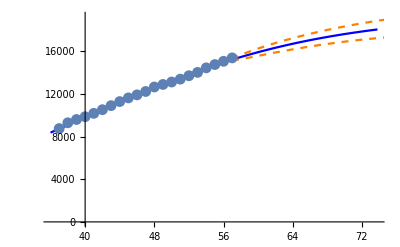
{-Graphics-,242.344,98.9939,319,-17.1075,78.7611}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,28,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,21,justtime];
```

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,28,justtime,jstartdate]]];
```

{981.19,4.49853,0.341492}

{1452.18,18.7219,0.227054}

{1452.18,18.7219,0.227054}

```mathematica
{"Russia",300,{133764.28972174952,345.7178233894532,0.17211220984196077},21,14,10,0}
```

```mathematica
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,8,0}
```

```mathematica
{name,trunc,cp0,lag,projt,bootl,drop}
```

```mathematica
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0}
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0}
```

```mathematica
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0}
```

```mathematica
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},21,14,10,0}
```

{Greece,50,{2469.73,97.9217,0.138165},21,14,10,0}

```mathematica
{"United Kingdom",200,{181106.79697173668,1069.9501757425367,0.1337539999625829},21,14,10,0}
{"Hungary",50,{3365.6444625267736,104.40659882066325,0.11408451894205024},28,14,10,0}
{"France",50,{177276.3912847858,1518.766119969371,0.13797898997605668},28,14,10,0}
{"Singapore",900,{21078.466173566427,299.80354836134035,0.17802870984146776},28,14,5,0}
{"Serbia",50,{10139.282988917936,113.99752601777078,0.1410478828462318},21,14,10,0}
{"Poland",50,{16098.415437312473,370.62817701093553,0.1065084233501309},21,14,10,0}
```

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

last tab: {21779.4,1446.22,0.0613938}

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

past errors : {{117.158,64.109,13.5794,16.8407,80.06,150.308,344.565,434.733,534.641,658.056},241.405}

boot tab : {{13627.2,229.936,0.131347},{11114.3,195.435,0.142952},{10824.6,192.529,0.144397},{10136.9,166.727,0.152786},{10413.6,178.982,0.14892},{10892.5,200.413,0.142841},{11475.1,232.693,0.1352},{13056.1,314.746,0.119793},{14215.8,393.753,0.109384},{15056.2,469.13,0.101855},{16576.3,584.856,0.0922481},{18811.3,722.096,0.0829107},{21650.4,856.053,0.0752707},{25305.2,1013.54,0.0680646},{28097.1,1131.12,0.063654},{28821.6,1227.54,0.0610384},{28616.2,1291.62,0.0596942},{28461.2,1361.97,0.0582909},{25710.5,1350.59,0.0598001},{23260.5,1284.86,0.0627113},{21267.1,1166.66,0.0670085},{20420.5,1097.63,0.0695436},{20210.8,1097.91,0.0698218},{20915.,1215.07,0.0664652},{21692.,1365.15,0.0627461},{23200.1,1614.66,0.0572315},{25449.5,1913.16,0.0514437}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

May 09

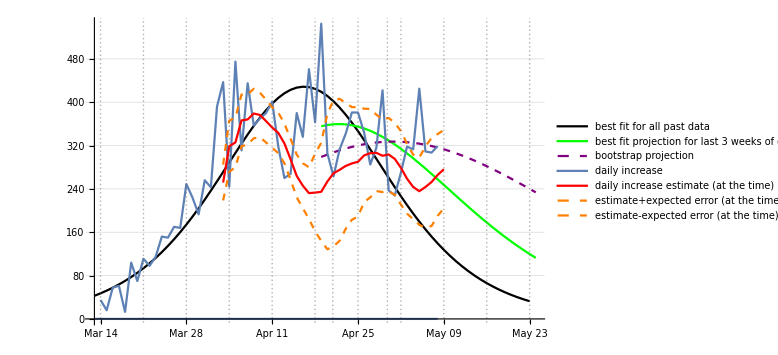

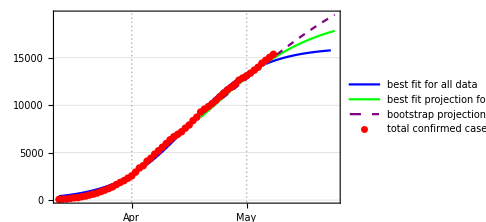

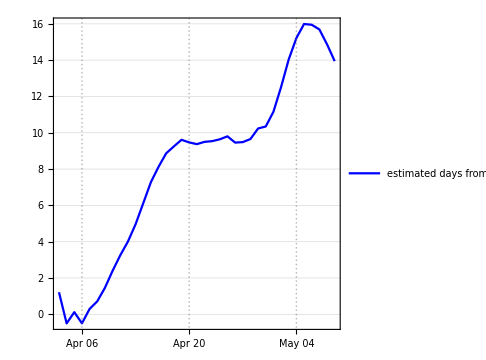

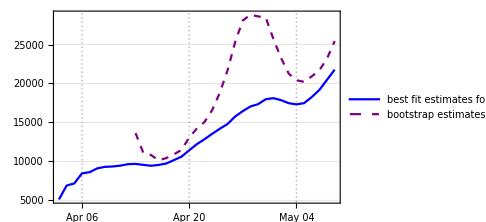

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,cboo}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,21,14,0,10,1000];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]]
jgraf
jloggraf
jdfpplot
jfinal
```